(*notebook for creation of MCNPX input file with ICRP reference phantoms; purpose: calculation of organ doses from CT, conventional radiography *)

(*slices in AF, 15M are counted from feet*)

(*SYNOPSIS: Debug version;
check the validity of collimator surface description;
Can be used to generate input file for calculator;
file fantomICRP.nb was prepared based on fantom_110ct_9.nb for NPCS 2021 conference and SAF calculations for pediatric phantom*)

```mathematica
(*TO DO:*)
```

```mathematica
(*fix AF "nsliMax":should not be 348 for AF;
test the calculation;
check the distance of phantom from the table to fit the trunk;
add write of "probabil.txt" file and MCNP execution;
test materials:could be errors in contents corresponding to element;
collimator,source and phantom lie in three different planes (2 layers 15M)
table should be moved using dy variable;
calculator:ns1 ns2 and nsliMax and nsliMin are redundant,as well as nc1 nc2 ncolmin ncolmax;
base voxel should be placed in the center of coordinate system
remove message when writing materials to 00m and 00m;
CT input file: currently the phantom is written prone and the phantom overlays the table even if patient lies prone; in Makarevich case the image surface was a plane; the table is however a cylinder, hence, it is harder to calculate the shift for table to fit the phantom*)
```

```mathematica
(*ERRORS*)
```

```mathematica
(*:if a fixed column is taken (nc=ncol or nc=1):ac should be written accordingly,then Left Adrenal with ac=1 is calculated;
collimator broke*)
```

### (*CHANGELOG*)

(*Previous version was saved on 25 April 2016;
changes on 15 November 2016: paths changed 
16 November 2016: indexes for reading complete phantom*)

(*2019 changes*)

(*7 Feb 2019: recent changes for thyroid;*)
(*29 Jul 2019: paths changed for /8core/debian 6.0*)
(*30 Jul 2019; fixed materials*)
(*5 Aug 2019: added shift over the table;*)
(*7 Aug 2019: added Carbon material;added R D U M cards;*)
(*12 Aug 2019: artificially changed the thickness of slice to 0.48*)
(*13 Aug 2019: introduced the CompressLine function*)

(*2020 changes*)

(*6 Feb 2020: finished writing short style lattice for MCNP; removed tally if no tissue is exposed;*)
(*22 Feb 2020: added setting of the volume for each organ*)
(*4 Mar 2020: fixed WriteMCNPCard to include three lines *)
(*9 Mar 2020: made a static long patient couch;*)
(*8 Apr 2020: minor correction to the procedure of writing the lattice;*)
(*4 Jun 2020: shifted phantom by 6 cm up to adjust it to the position of CT couch*)
(*18 Jun 2020: 
 and nslimin are extremal;*)
(*26 Oct 2020: adding gender*)

```mathematica
(*2021 changes*)
```

```mathematica
(*3 May 2021; added more comments*)
```

(*13 Jul 2021: started Ages: added voxel count, sizes; *)

(*14 Jul 2021: MAJOR REVISION: removed directory to phantoms: from now they should be placed in the notebook directory; amended synopsis*)

(*15 Jul 2021: added monitoring of processing lattice*)

(*16 Jul 2021: united with profile structure.nb*)

(*19 July 2021: renamed into FantomICRP; replaced old style voxel construction to Choonsik style*)

(*20 Jul 2021: fixed center of the voxel universe*)

(*23 Jul 2021: fixed the accuracy of azVupB variable*)

(*28 Jul 2021: debug material write etc. for adults*)

(*2 Aug 2021 fix write of rows in lattice*)

```mathematica
(*6 Jan 2021 changed writing of sagittal image; they were later removed*)
```

```mathematica
(*2022 changes*)
```

```mathematica
(*5 Aug 2022: cleanup*)
```

```mathematica
(*14 Sep 2022: paths changed; fixed write of air inside the box; fixed write of surfaces in case of CT;*)
```

```mathematica
Needs["Units`"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/media/arkady/D07C278B7C276B82/1/backup/2020/17 Jun SAF/fantom110c-9ct

```mathematica
(*TAMSIP*)
```

```mathematica
adresSpectrum="/media/arkady/D07C278B7C276B82/1/work/spectra/TASMIP_Source"
```

/media/arkady/D07C278B7C276B82/1/work/spectra/TASMIP_Source

```mathematica
voltage=80;
```

```mathematica
(*!!!CHANGE AppertZ TO 0.01 cm AND AppertX to 40 cm to get horizontal cross-section;*)
AppertZ={40};(*cm*)
AppertX={30};(*cm*)
(*!!!*)
RIP={150};(*cm*)
proection={"PA"};
```

```mathematica
Nproect=proection[[1]];
```

```mathematica
WriteMCNPCard[Line1_] := Module[{Line2, Line1M(*list for the words in Line*), i, NLines,Line3,NsymoblsinLine},NsymoblsinLine=73(*80-5-?*); Line3="";If[StringLength[Line1] >NsymoblsinLine, NLines = Quotient[StringLength[Line1], NsymoblsinLine]; Line1M = StringSplit[Line1, {" ","\n"}]; i =1;
Do[  Line2="";While[If[i>Length[Line1M],False,StringLength[Line2] <  NsymoblsinLine - StringLength[Line1M[[i]]] ],Line2 =StringTrim[ Line2 <> " " <> Line1M[[i]]];i = i +1;];Line3=StringTrim[Line3~~"     "~~Line2]~~"\n", {j, NLines +1}];Line3=StringTake[Line3,StringLength[Line3]-1];Return[Line3](*Find the last space before 80th position and split line into two at the position of the space*),Return[Line1]]];
```

```mathematica
(*turns 140 140 into 140 r*)
CompressLine[DummyArr_]:=Module[{DummyArrLen,DummyArrcurrent,times,Strout},DummyArrLen=Length[DummyArr];DummyArrcurrent=DummyArr[[1]];times=0;Strout="";Do[If[DummyArrcurrent==DummyArr[[i]],times++,
Strout=Strout~~" "~~ToString[DummyArrcurrent]~~" "~~Switch[times,0,"",1,"r ",_,ToString[times]~~"r "];DummyArrcurrent=DummyArr[[i]];times=0],{i,2,DummyArrLen}];Strout=Strout~~" "~~ToString[DummyArrcurrent]~~" "~~Switch[times,0,"",1,"r ",_,ToString[times]~~"r "]]
```

```mathematica
CT=True;(*Boolean: True or False*)
```

```mathematica
SplitFiles=True;(*Boolean: True or False;if true, .lat is written separately; if false, lattice is written into the main file*)
```

```mathematica
(*Hands=False;*)(*Boolean: True or False; not implemented?*)
```

```mathematica
Phantom="AF";(*AF; AM; 00M; 00F; 01M; 01F; 05M; 05F; 10M; 10F; 15M; 15F*)
```

```mathematica
(*ProceduresLst={"Lungs"};*)(*Precedures list is stored in work.txt file*)
```

```mathematica
ProceduresLst={Phantom};
```

```mathematica
SetDirectory[NotebookDirectory[]<>Phantom]
```

/media/arkady/D07C278B7C276B82/1/backup/2020/17 Jun SAF/fantom110c-9ct/AF

```mathematica
(*столбцы - columns*)
```

```mathematica
ncol=Switch[Phantom,"AM",254,"AF",299,"00M"|"00F",345,"01M"|"01F",393,"05M"|"05F"|"10M"|"10F",419,"15M",407,_,401]
```

299

```mathematica
nrow=Switch[Phantom,"AM",127,"AF",137,"00M"|"00F",211,"01M"|"01F",248,"05M"|"05F",230,"10M"|"10F",226,"15M",225,_,236]
```

137

```mathematica
nsli=Switch[Phantom,"AM",222,"AF",348,"00M"|"00F",716,"01M"|"01F",546,"05M"|"05F",572,"10M"|"10F",576,"15M",586,_,571]
```

348

```mathematica
nn2= nrow   ncol
```

40963

```mathematica
(*voxelres cm*)
```

```mathematica
dvcol=Switch[Phantom,"AM",0.2137,"AF",0.1775,"00M"|"00F"|"01M"|"01F",0.0663,"05M"|"05F",0.085,"10M"|"10F",0.099,"15M",0.125,_,0.12]
```

0.1775

```mathematica
dvrow=dvcol;(*should be removed only if not used for Mass change*)
```

```mathematica
(*Slice thickness, cm;AM 1st, AF - 2nd*)
```

```mathematica
dvsl=Switch[Phantom,"AM",0.8,"AF",0.484,"00M"|"00F",0.0663,"01M"|"01F",0.14,"05M"|"05F",0.1928,"10M"|"10F",0.2425,"15M",0.2832,_,0.2828]
```

0.484

```mathematica
Kcent=0(*counted from feet*)
```

0

```mathematica
Zcent=(nsli-Kcent) dvsl(*cm from top; used for determination of sdef position;*)
```

168.432

```mathematica
(*Zcentr=Zcent*)(*was an index for CT: to calculate the row of coefficients from 1 to 160 cm*)
```

## (* reading of initial phantom *)

```mathematica
(* Creation of Surfaces and Source and Tally *)
```

```mathematica
(*scatteredfield=15.55;*)(*cm; guess from Makarevich;which projection?*)
```

```mathematica
ImageGap=1;(*somewhere in report it was 5 cm, but in CreatePhantomMale.nb it is 1 from skin plane, not from box*)
```

```mathematica
(*setting the position of the source depending on the projection*)
srcx=0;(*only two projections -AP and PA, we make x position constant*)
```

```mathematica
If[Nproect=="AP",srcy=-(RIP[[1]]-3-ImageGap);vec=" vec=0 1 0 ",srcy=RIP[[1]]-3-ImageGap;vec=" vec= 0 -1 0 "]
```

vec= 0 -1 0

```mathematica
eps=.001;(*small parameter for lattice to include less than the volume of the voxels*)
```

```mathematica
dvslB=dvsl-  eps;(*a value less than the size of voxel along z axis*)
```

```mathematica
(*5.781658 is arbitrary value was selected in ~2017 to center phantom head in CT axis;3 cm for the line of phantom to lie below the table;6.36325 is the solution of system of equations {(x-0)^2+(y-43)^2==51.1^2,x==-13.2087}*)
```

```mathematica
dy=5.78165+(6.36325)-3(*for head 5.78165;*)(*for CT shift?*)
```

9.1449

```mathematica
dx=0;
```

(*for CT shift?*)

```mathematica
dz=0.;163.544(*AF*)
```

163.544

```mathematica
If[Length[StringPosition[Phantom,"A"]]>=1,fantom1=ReadList[Phantom~~".dat",Number,RecordSeparators->{"\n","   "}];,fantom1=ReadList[Phantom~~"_ascii.dat",Number,RecordSeparators->{"\n"," "}];]
```

```mathematica
nsliMin=1;(*Round[Kcent-(AppertZ[[1]]/2+scatteredfield)/dvsl]:;nsli-19:2018 female calculation*)
```

```mathematica
Kcent-(AppertZ⟦1⟧/2+scatteredfield)/dvsl
```

-2.06612 (20+scatteredfield)

```mathematica
(*nsliMin=nsli-172*)(*to include all Skin,trunk;292*)
```

```mathematica
(*Min[Round[Kcent+(AppertZ[[1]]/2+scatteredfield)/dvsl],nsli]*)
```

```mathematica
(*nsli/2 is OK for 15M*)
```

```mathematica
nsliMax=nsli
```

348

```mathematica
min(Round[(AppertZ⟦1⟧/2+scatteredfield)/dvsl+Kcent],nsli)
```

Min[348,Round[2.06612 (20+scatteredfield)]]

```mathematica
(* 3D array of voxels  for given sections;  *)
```

```mathematica
(* x-anterior posterior-back row, y-left-right-column, z -down-up -slides -*)
```

```mathematica
(*coordinate system is right:x(columns) goes from spine to hand;y(rows) goes from spine to nose;z goes from legs to top*)
```

```mathematica
ncolMin=1;(*should be 1*)
ncolMax=ncol;(*should be ncol*)
```

```mathematica
ac=ConstantArray[1,{ ncolMax-ncolMin+1, nrow ,nsliMax-nsliMin+1}];
```

```mathematica
(*Do[Switch[
fantom1[[i] ],0,
fantom2[[i-nrow (nsliMin-1) (ncolMax-ncolMin+1)]]=140,141,fantom2[[i-nrow (nsliMin-1) (ncolMax-ncolMin+1)]]=122,_,
 fantom2[[i-nrow (nsliMin-1) (ncolMax-ncolMin+1)]]=fantom1[[i]]
]
,{i,nrow (nsliMin-1) (ncolMax-ncolMin+1)+1,nrow nsliMax (ncolMax-ncolMin+1)}]  ; *)(*fantom2 should be kept*)
```

```mathematica
Timing[Do[ 
        Do[    
                           Do[    iw=nn2  (isl-1) + ncol* (ir-1)  +ic;
                                 Switch[
fantom1[[iw] ],0,
 ac[[ic]][[ir]][[isl-nsliMin+1]]=140,141,ac[[ic]][[ir]][[isl-nsliMin+1]]=122,_,
  ac[[ic]][[ir]][[isl-nsliMin+1]]=fantom1[[iw]]
]
                            , {ic,ncolMin-ncolMin+1,ncolMax-ncolMin+1}]
         ,{ir,1,nrow}];Print["end processing slice " ,isl];
,{isl,nsliMin,nsliMax}]  ; 
orgSections=Union[Flatten[ac]];]
```

end processing slice 1

end processing slice 2

end processing slice 3

end processing slice 4

end processing slice 5

end processing slice 6

end processing slice 7

end processing slice 8

end processing slice 9

end processing slice 10

end processing slice 11

end processing slice 12

end processing slice 13

end processing slice 14

end processing slice 15

end processing slice 16

end processing slice 17

end processing slice 18

end processing slice 19

end processing slice 20

end processing slice 21

end processing slice 22

end processing slice 23

end processing slice 24

end processing slice 25

end processing slice 26

end processing slice 27

end processing slice 28

end processing slice 29

end processing slice 30

end processing slice 31

end processing slice 32

end processing slice 33

end processing slice 34

end processing slice 35

end processing slice 36

end processing slice 37

end processing slice 38

end processing slice 39

end processing slice 40

end processing slice 41

end processing slice 42

end processing slice 43

end processing slice 44

end processing slice 45

end processing slice 46

end processing slice 47

end processing slice 48

end processing slice 49

end processing slice 50

end processing slice 51

end processing slice 52

end processing slice 53

end processing slice 54

end processing slice 55

end processing slice 56

end processing slice 57

end processing slice 58

end processing slice 59

end processing slice 60

end processing slice 61

end processing slice 62

end processing slice 63

end processing slice 64

end processing slice 65

end processing slice 66

end processing slice 67

end processing slice 68

end processing slice 69

end processing slice 70

end processing slice 71

end processing slice 72

end processing slice 73

end processing slice 74

end processing slice 75

end processing slice 76

end processing slice 77

end processing slice 78

end processing slice 79

end processing slice 80

end processing slice 81

end processing slice 82

end processing slice 83

end processing slice 84

end processing slice 85

end processing slice 86

end processing slice 87

end processing slice 88

end processing slice 89

end processing slice 90

end processing slice 91

end processing slice 92

end processing slice 93

end processing slice 94

end processing slice 95

end processing slice 96

end processing slice 97

end processing slice 98

end processing slice 99

end processing slice 100

end processing slice 101

end processing slice 102

end processing slice 103

end processing slice 104

end processing slice 105

end processing slice 106

end processing slice 107

end processing slice 108

end processing slice 109

end processing slice 110

end processing slice 111

end processing slice 112

end processing slice 113

end processing slice 114

end processing slice 115

end processing slice 116

end processing slice 117

end processing slice 118

end processing slice 119

end processing slice 120

end processing slice 121

end processing slice 122

end processing slice 123

end processing slice 124

end processing slice 125

end processing slice 126

end processing slice 127

end processing slice 128

end processing slice 129

end processing slice 130

end processing slice 131

end processing slice 132

end processing slice 133

end processing slice 134

end processing slice 135

end processing slice 136

end processing slice 137

end processing slice 138

end processing slice 139

end processing slice 140

end processing slice 141

end processing slice 142

end processing slice 143

end processing slice 144

end processing slice 145

end processing slice 146

end processing slice 147

end processing slice 148

end processing slice 149

end processing slice 150

end processing slice 151

end processing slice 152

end processing slice 153

end processing slice 154

end processing slice 155

end processing slice 156

end processing slice 157

end processing slice 158

end processing slice 159

end processing slice 160

end processing slice 161

end processing slice 162

end processing slice 163

end processing slice 164

end processing slice 165

end processing slice 166

end processing slice 167

end processing slice 168

end processing slice 169

end processing slice 170

end processing slice 171

end processing slice 172

end processing slice 173

end processing slice 174

end processing slice 175

end processing slice 176

end processing slice 177

end processing slice 178

end processing slice 179

end processing slice 180

end processing slice 181

end processing slice 182

end processing slice 183

end processing slice 184

end processing slice 185

end processing slice 186

end processing slice 187

end processing slice 188

end processing slice 189

end processing slice 190

end processing slice 191

end processing slice 192

end processing slice 193

end processing slice 194

end processing slice 195

end processing slice 196

end processing slice 197

end processing slice 198

end processing slice 199

end processing slice 200

end processing slice 201

end processing slice 202

end processing slice 203

end processing slice 204

end processing slice 205

end processing slice 206

end processing slice 207

end processing slice 208

end processing slice 209

end processing slice 210

end processing slice 211

end processing slice 212

end processing slice 213

end processing slice 214

end processing slice 215

end processing slice 216

end processing slice 217

end processing slice 218

end processing slice 219

end processing slice 220

end processing slice 221

end processing slice 222

end processing slice 223

end processing slice 224

end processing slice 225

end processing slice 226

end processing slice 227

end processing slice 228

end processing slice 229

end processing slice 230

end processing slice 231

end processing slice 232

end processing slice 233

end processing slice 234

end processing slice 235

end processing slice 236

end processing slice 237

end processing slice 238

end processing slice 239

end processing slice 240

end processing slice 241

end processing slice 242

end processing slice 243

end processing slice 244

end processing slice 245

end processing slice 246

end processing slice 247

end processing slice 248

end processing slice 249

end processing slice 250

end processing slice 251

end processing slice 252

end processing slice 253

end processing slice 254

end processing slice 255

end processing slice 256

end processing slice 257

end processing slice 258

end processing slice 259

end processing slice 260

end processing slice 261

end processing slice 262

end processing slice 263

end processing slice 264

end processing slice 265

end processing slice 266

end processing slice 267

end processing slice 268

end processing slice 269

end processing slice 270

end processing slice 271

end processing slice 272

end processing slice 273

end processing slice 274

end processing slice 275

end processing slice 276

end processing slice 277

end processing slice 278

end processing slice 279

end processing slice 280

end processing slice 281

end processing slice 282

end processing slice 283

end processing slice 284

end processing slice 285

end processing slice 286

end processing slice 287

end processing slice 288

end processing slice 289

end processing slice 290

end processing slice 291

end processing slice 292

end processing slice 293

end processing slice 294

end processing slice 295

end processing slice 296

end processing slice 297

end processing slice 298

end processing slice 299

end processing slice 300

end processing slice 301

end processing slice 302

end processing slice 303

end processing slice 304

end processing slice 305

end processing slice 306

end processing slice 307

end processing slice 308

end processing slice 309

end processing slice 310

end processing slice 311

end processing slice 312

end processing slice 313

end processing slice 314

end processing slice 315

end processing slice 316

end processing slice 317

end processing slice 318

end processing slice 319

end processing slice 320

end processing slice 321

end processing slice 322

end processing slice 323

end processing slice 324

end processing slice 325

end processing slice 326

end processing slice 327

end processing slice 328

end processing slice 329

end processing slice 330

end processing slice 331

end processing slice 332

end processing slice 333

end processing slice 334

end processing slice 335

end processing slice 336

end processing slice 337

end processing slice 338

end processing slice 339

end processing slice 340

end processing slice 341

end processing slice 342

end processing slice 343

end processing slice 344

end processing slice 345

end processing slice 346

end processing slice 347

end processing slice 348

{103.336,Null}

```mathematica
(* Selection organs of given sections *)
cell0= Import[Phantom<>"_organs.dat","Table"];
cell={};
Do[   
 Do[ If[ orgSections[[ik]]==cell0[[io]][[1]],AppendTo[ cell,cell0[[io]]],Null],{ik,1,Length[orgSections]}]
,{io,5,Length[cell0]}]
```

```mathematica
(*AF*)volcell={365,463,275,910,1152,250,509,553,375,14995,2675,5731,3846,6193,1331,3491,3098,1375,5299,5355,2248,3555,4275,1110,2227,13785,21964,8462,14105,2644,7940,10252,3709,21137,34425,5865,5866,15868,1535,1912,8875,26316,5563,15563,4114,5632,2421,4206,6960,15283,5281,14636,8754,57,2890,941,18696,5873,13271,81192,10355,6429,10355,6429,13,456,12,456,652,2913,8828,14503,37833,17656,5675,6306,3468,3783,3468,1892,5675,3153,2838,5044,1576,15614,22891,6535,2334,467,5488,1960,392,87437,3664,64218,2615,80402,85,246,164,3671,248,624,25105,532007,95236,440618,2228,347,347,7495,38,61165,814763,140986,611935,2228,2229,10432,60411,28248,64641,1186,8197,954,1273,1072,2595,191,478,477,2522,12611,5094,2439}
```

{365,463,275,910,1152,250,509,553,375,14995,2675,5731,3846,6193,1331,3491,3098,1375,5299,5355,2248,3555,4275,1110,2227,13785,21964,8462,14105,2644,7940,10252,3709,21137,34425,5865,5866,15868,1535,1912,8875,26316,5563,15563,4114,5632,2421,4206,6960,15283,5281,14636,8754,57,2890,941,18696,5873,13271,81192,10355,6429,10355,6429,13,456,12,456,652,2913,8828,14503,37833,17656,5675,6306,3468,3783,3468,1892,5675,3153,2838,5044,1576,15614,22891,6535,2334,467,5488,1960,392,87437,3664,64218,2615,80402,85,246,164,3671,248,624,25105,532007,95236,440618,2228,347,347,7495,38,61165,814763,140986,611935,2228,2229,10432,60411,28248,64641,1186,8197,954,1273,1072,2595,191,478,477,2522,12611,5094,2439}

```mathematica
Timing[volcell=Table[Count[Take[fantom1,{nrow (nsliMin-1) (ncolMax-ncolMin+1)+1,nrow nsliMax (ncolMax-ncolMin+1)}],cell[[i,1]]],{i,Length[cell]}]]
```

{101.356,{365,463,275,910,1152,250,509,553,375,14995,2675,5731,3846,6193,1331,3491,3098,1375,5299,5355,2248,3555,4275,1110,2227,13785,21964,8462,14105,2644,7940,10252,3709,21137,34425,5865,5866,15868,1535,1912,8875,26316,5563,15563,4114,5632,2421,4206,6960,15283,5281,14636,8754,57,2890,941,18696,5873,13271,81192,10355,6429,10355,6429,13,456,12,456,652,2913,8828,14503,37833,17656,5675,6306,3468,3783,3468,1892,5675,3153,2838,5044,1576,15614,22891,6535,2334,467,5488,1960,392,87437,3664,64218,2615,80402,85,246,164,3671,248,624,25105,532007,95236,440618,2228,347,347,7495,38,61165,814763,140986,611935,2228,2229,10432,60411,28248,64641,1186,8197,954,1273,1072,2595,191,478,477,2522,12611,5094,2439}}

```mathematica
(* READING OF SPECTRUM *)
```

```mathematica
(*recovered from "fantom110c-8ct.nb" 7 Feb 2019*)
```

```mathematica
Directory[]
```

/media/arkady/D07C278B7C276B82/1/backup/2020/17 Jun SAF/fantom110c-9ct/AF

```mathematica
spAdress={"x100_Al2p5_W.txt","x105_Al2p5_W.txt","x109_Al1p4_W.txt","x109_Al2p5_W.txt",
"x109_W.txt","x110_Al2p5_W.txt","x115_Al2p5_W.txt","x120_Al2p5_W.txt",
"x125_Al2p5_W.txt","x130_Al2p5_W.txt","x135_Al2p5_W.txt","x140_Al2p5_W.txt",
"x30_Al2p5_W.txt","x35_Al2p5_W.txt","x40_Al2p5_W.txt","x40_Re_m.txt",
"x40_W_m.txt","x40_W.txt","x45_Al2p5_W.txt","x50_Al2p5_W.txt","x55_Al2p5_W.txt",
"x60_Al1p4_W.txt","x60_Al2p5_W.txt","x60_W.txt","x63_Al1p4_W.txt","x63_Al2p5_W.txt",
"x63_W.txt","x65_Al2p5_W.txt","x70_Al1p4_W.txt","x70_Al2p5_W.txt","x70_Al3_W.txt","x75_Al2p5_W.txt",
"x77_Al1p4_W.txt","x77_Al2p5_W.txt","x77_W.txt","x80_Al2p5_W.txt","x80_Al3_W.txt","x81_Al1p4_W.txt",
"x81_Al2p5_W.txt","x85_Al1p4_W.txt","x85_Al2p5_W.txt","x85_W.txt","x90_Al1p4_W.txt",
"x90_Al2p5_W.txt","x90_W.txt","x95_Al2p5_W.txt","x96_Al1p4_W.txt","x96_Al2p5_W.txt","x110_Al0p5_W.txt","x110_Al1p4_W.txt","x110_Al2p5_W.txt","x110_Al3_W.txt","x110_Al4_W.txt","x110_Al5_W.txt","x110_Al6_W.txt","x110_W.txt","x120_Al0p5_W.txt","x120_Al1p4_W.txt","x120_Al2p5_W.txt","x120_Al3_W.txt","x120_Al4_W.txt","x120_Al5_W.txt","x120_Al6_W.txt","x120_W.txt"};
```

```mathematica
vv0=voltage;    (* ParametersRegInsp[[iq]][[7]];*)
vv1=voltage;   (* ParametersRegInsp[[iq]][[8]]; *)
Print["V0==",vv0,"  V1==",vv1];
```

V0==80  V1==80

```mathematica
ener=IntegerPart[vv0];
adresSp="x"~~ToString[ener]~~"_";
Clear[fu];fu[x_]:=StringTake[x,{2,4}];
If[ener<100,EEE=ToString[ener]~~"_",EEE=ToString[ener]];
enerArray=Map[fu,spAdress];
cc=Flatten[Position[enerArray,EEE]];
adresFile=Part[spAdress,cc];
dAluminium="3";(*!!! fixed filter*)
If[dAluminium≠ 0,If[dAluminium=="2p5",at=StringReplacePart[dAluminium,"p",{2,2}],at=dAluminium];adresSp=adresSp~~"Al"~~at~~"_W",
adresSp=adresSp~~"W"];
adresSp=adresSp~~".txt";val= SetDirectory[adresSpectrum] ;
If[Position[spAdress,adresSp]!={},If[TrueQ[val==Symbol["$Failed"]],Print["SpectrumFile is absent"],Print["SPECTRUM Ok"];],Print["SpectrumFile is absent 2"]];


Print[%];
iop=OpenRead[adresSp];

aw1= Read[iop,Record];
bw1= Read[iop,Record];
spectrum={};
aw= Read[iop,Real];bw= Read[iop,Number];
While[aw≠ "EOF",AppendTo[spectrum,{aw*10^-6,bw}];aw= Read[iop,Real];bw= Read[iop,Number]];Close[iop];
Print[%];
```

SPECTRUM Ok

Null

x80_Al3_W.txt

```mathematica
SetDirectory[NotebookDirectory[]<>Phantom];
```

```mathematica
(* Creation of Input File *)
```

```mathematica
(* Creation of Cells *)
```

```mathematica
(* Media to be used *)
numMed={};
Do[ AppendTo[numMed,cell[[ii]][[-2]]];
  ,{ii,1,Length[cell]}]
```

```mathematica
numMed=Union[numMed]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53}

```mathematica
box="num box of fantom";
```

```mathematica
(*nr1=-68 for AF*)
```

```mathematica
nr2=Round[nrow/2]
```

68

```mathematica
nr1=nr2-nrow+1
```

-68

```mathematica
(*nr2=Round[nrow/2]*)(*if nrow is odd, seems OK; 4 Aug 2021*)
```

```mathematica
ns1=-nsliMax+nsliMin
```

-347

```mathematica
ns2=0;
```

```mathematica
nc1=Round[N[ncol/2]]-ncolMax(*??? check AM *)
```

-149

```mathematica
nc2=Round[N[ncol/2]]-ncolMin
```

149

```mathematica
(* Start of writing into inp-file *)
```

```mathematica
Directory[]
```

/media/arkady/D07C278B7C276B82/1/backup/2020/17 Jun SAF/fantom110c-9ct/AF

```mathematica
Streams[](*diagnostics*)
```

{OutputStream[…],OutputStream[…]}

```mathematica
ipp=OpenWrite[ProceduresLst[[1]]~~"_"~~ToString[Zcent]];
```

```mathematica
WriteLine[ipp,"phantom_for_*F8_calculations  "~~ToString[Length[volcell]]]
```

```mathematica
WriteLine[ipp,"c "~~Phantom];
```

```mathematica
If[CT,WriteLine[ipp,"c mode=CT"],WriteLine[ipp,"c mode=calculator; Date:"~~ToString[DateValue["Day"]]~~" "~~ToString[DateValue["MonthName"]]~~" "~~ToString[DateValue["Year"]]~~"; Kcent="~~ToString[Kcent]]]
```

```mathematica
(*If[CT,WriteString[ipp," Zcent="<>ToString[Zcent]],WriteString[ipp," Zcent="<>ToString[Zcent]]];*)
```

```mathematica
(*table or collimator*)
```

```mathematica
If[StringPosition[Phantom,"A"]≠{},numAir="53",numAir="57"]
```

53

```mathematica
If[CT,WriteString[ipp,"209 54     -1.4         8 -9 210 -211 -12 imp:p=1 vol=1 $ inner table shell\n    210 54      -1.4 13 -14 210 -211 -12 imp:p=1 vol=1 $ outer table shell\n"],WriteString[ipp, "160 80 -11.3 -160 170 imp:p=1 vol=1\n170 "<>numAir<>" -.001 -170 imp:p=1 vol=1\n"]];
```

```mathematica
Do[   ww=cell[[ic]];work="    "~~ToString[cell[[ic]][[1]]]~~"  ";word="  $ ";ss=-1;
              Do[ If[ NumberQ[ ww[[ik]]] ,If[cell[[ic,1]]==140,work="140 "<>numAir<>" -.001 ",ss=ss*(-1);work=work~~ToString[ss*ww[[ik]]]~~"   "],word=word~~ToString[ww[[ik]]]~~" "] ,{ik,2,Length[ww]}];
work=work~~"-32  u="~~ToString[cell[[ic]][[1]]]~~"     imp:p=1 vol="~~ToString[dvrow dvcol dvsl volcell[[ic]]]~~word~~"\n";
WriteString[ipp,work]
,{ic,1,Length[cell]}];
```

```mathematica
If[CT,WriteString[ipp,"200 "<>numAir<>" -.001  40 -41 50 -51 60 -61 (-8:9:-210:211:12) (-13:14:-210:211:12) "];WriteString[ipp,"&\nimp:p=1 vol=1 fill=200 $ BOX\n198 "<>numAir<>" -.001 -70 #200 (-8:9:-210:211:12) (-13:14:-210:211:12)  imp:p=1&\n vol=1$ inside vac Sphere\n"];, WriteString[ipp,"200 "<>numAir<>" -.001 40 -41 50 -51 60 -61 170 160&\nimp:p=1 vol=1 fill=200 $ BOX\n198 "<>numAir<>" -.001 -70 #200 170 160 imp:p=1&\n vol=1$ inside vac Sphere\n"]]
```

```mathematica
WriteLine[ipp,"199 0 70 imp:p=0 vol=0"];
```

```mathematica
(* Creation of Lattice *)
```

```mathematica
If[SplitFiles,latfilename=ToLowerCase[Phantom]~~".lat";WriteLine[ipp,"c read external file with "~~ToString[1-ns1]~~" slices"];WriteLine[ipp,"read file="~~latfilename~~" noecho"];If[Length[Position[FileNames[],latfilename]]==0,LatticeFileStream=OpenWrite[latfilename],LatticeFileStream="stderr";];,LatticeFileStream=ipp;]
```

```mathematica
WriteString[LatticeFileStream,"150 "<>numAir~~" -.001 -111 110 -121 120 -131 130 u=200 imp:p=1 vol=1\n"~~"      "~~"lat=1  "~~
"fill="~~ToString[nc1]~~":"~~ToString[nc2]~~"  "~~ToString[nr1]~~":"~~ToString[nr2]~~"  "~~ToString[ns1]~~
":"~~ToString[ns2]~~"  $ the lattice "~~"\n"];
```

```mathematica
(*Do[www1="";Do[www="";Do[ www=www~~ToString[ac[[ic]][[ir]][[isl]]]~~" ",{ic,ncolMax,ncolMin,-1}];www=CompressLine[StringSplit[www," "]];www=StringReplace[www,"  "->" "];www1=www1~~"     "~~WriteMCNPCard[www];www="\nc end row "~~ToString[ir]~~"\n";www1=www1~~www,{ir,nrow,1,-1}];www="c end slice "~~ToString[isl]~~"\n";www1=www1~~www;WriteString[LatticeFileStream,www1];
,{isl,1,nsliMax-nsliMin+1}] ;*)
```

```mathematica
Timing[Do[www1 = " "; Do[               www = "       ";          
                             Do[ www = www ~~ " " ~~ ToString[ac[[ic,ir,isl]]];
                            If[StringLength[www] >= 75, www = www ~~ "\n"; www1 = www1 ~~ www; www = "       "]   
                                  , {ic, ncolMin, ncolMax}];
                                  If[StringLength[www]  >  8, www = www ~~ "\n"; www1 = www1 ~~ www];
   www = "c end row" ~~ ToString[ir] ~~ "\n";
   www1 = www1 ~~ www
            , {ir, 1, nrow}];
  www = "c end slice" ~~ ToString[isl] ~~ "\n";
  www1 = www1 ~~ www;
  
  WriteString[LatticeFileStream, www1]
  , {isl, 1, nsliMax - nsliMin + 1}] ;]
```

{147.568,Null}

```mathematica
(*creation of an array *)
```

```mathematica
(*Timing[densityInd=Table[Table[Table[Last[
cell[[
Position[cell[[All,1]],ac[[ic,ir,isl]]][[1,1]]
]]
], {ic, ncolMin, ncolMax}], {ir, 1, nrow}],{isl, 1, nsliMax - nsliMin + 1}] ;]*)
```

```mathematica
{1208.716,Null}(*15M 4 core*)
```

{1208.72,Null}

```mathematica
(*Possibly move this block after the phantom write*)
```

```mathematica
(*for electron whole body source;AF*)(*Cases[ac[[ic,ir,isl]],{val_/;(val<13||val>52)&&(val<54||val>56)}]*)
```

```mathematica
(*Timing[ipp4=OpenWrite["body_sdef_cell_sp_par_3.dat"];WriteLine[ipp4,"sp4 &"];Do[Do[Do[If[ac[[ic,ir,isl]]≠140,If[(ac[[ic,ir,isl]]<13||ac[[ic,ir,isl]]>56),sp=ToString[densityInd[[isl,ir,ic]]],sp="0"];Timing[WriteLine[ipp4,sp<>" &"]]];, {ic, ncolMin, ncolMax}], {ir, 1, nrow}],{isl, 1,nsliMax - nsliMin +  1}] ;Close[ipp4]]*)
```

```mathematica
If[SplitFiles,If[Length[Position[FileNames[],latfilename]]==0,Close[LatticeFileStream]];]
```

```mathematica
(*!!! check the validity of resulting phantom*)
```

```mathematica
(* Creation of Surfaces and Source *)
```

```mathematica
(* dimensions of Base VOXEL *)
```

```mathematica
(*"V" for Voxel, "B" for base*)
```

```mathematica
axVB=dvcol(*AF phantom has odd number of voxels in that direction, so the voxel lies in the middle of X axis*)
```

0.1775

```mathematica
ayVB=dvrow
```

0.1775

```mathematica
azVdownB=SetPrecision[dvsl*nsliMax-dz,7]
```

168.432

```mathematica
azVupB=SetPrecision[dvsl (nsliMax+1)-dz,7]
```

168.916

```mathematica
SetPrecision[azVupB-azVdownB,14]
```

0.48400000000001

```mathematica
(* dimensions of BOX *)
```

```mathematica
(*axB is from the positive side of the col count*)
```

```mathematica
axB=dvcol nc1+eps
```

-26.4465

```mathematica
(*along X axis*)
```

```mathematica
axB1=ToString[dvcol (nc2+1)-eps]
```

26.624

```mathematica
ayB=ToString[dvrow nr1 +eps]
```

-12.069

```mathematica
ayB1=ToString[dvrow (nr2+1)-eps]
```

12.2465

```mathematica
azB1=dvsl*nsliMin-dz+eps
```

0.485

```mathematica
azB2=dvsl (nsliMax+1)-eps-dz
```

168.915

```mathematica
(*position of z plane which corresponds to the position of base voxel*)
```

```mathematica
If[azVupB<azB2,MessageDialog["Upper border of voxel "~~ToString[azVupB]~~" is lower than the border of the box "~~ToString[azB2]]]
```

```mathematica
If[azVdownB+(azVupB-azVdownB) ns1>azB1,MessageDialog["Lower border of voxel is above the lower border of the box"]]
```

```mathematica
(*azB2=ToString[Round[(dvsl (nsliMax)+dvslB/2.)-dvslB/100.-0.0001-dz,0.01]]*)
```

```mathematica
(* dimensions of VACCUUM SPHERA *)
```

```mathematica
radVacSph=Max[Sqrt[((dvcol ncol)/2.)^2 + ((dvrow nrow)/2.)^2+ ((dvsl nsli)/2.)^2],250](*for pediatric phantoms collimator appears outside the sphere*)
```

250

```mathematica
WriteLine[ipp,""]
```

```mathematica
(*creation of CT couch*)
```

```mathematica
If[CT,WriteString[ipp,"1 rcc 0 0 -30 0 0 50 75 $ universe\n8 c/z 0 43 51.1\n9 c/z 0 43 51.4\n210 pz "~~ToString[Round[(dvsl)-dvslB/2. +dvslB/1000.+0.0001-dz,0.01]]~~"\n211 pz "~~ToString[azB2]~~"\n12 py -3\n13  c/z 0 23.3 35\n14  c/z 0 23.3 35.3\n"]]
```

```mathematica
(* creation of voxel *)
```

```mathematica
y0=dvrow/2.(*position of center of base voxel*)
```

0.08875

```mathematica
z0=(azVupB+azVdownB)/2
```

168.674

```mathematica
R=√((Evaluate[ToExpression[axVB]])^2+(azVupB-azVdownB)^2/4+((y0-dvrow/2.)-Evaluate[ToExpression[ayVB]])^2/4)+eps
```

0.313965

```mathematica
WriteLine[ipp,"32 s 0 "~~ToString[y0]~~" "~~ToString[z0]~~" "~~ToString[R]~~"$ voxel"];
```

```mathematica
(* creation of Base voxel *)
```

```mathematica
WriteLine[ipp,"c  Base voxel"]
```

```mathematica
WriteLine[ipp,"110 px 0 $ voxel surf 1; column"]
```

```mathematica
WriteLine[ipp,"111 px "~~ToString[axVB]~~" $ voxel surf 2; column"]
```

```mathematica
WriteLine[ipp,"120 py 0 $ voxel surf 3; row"]
```

```mathematica
WriteLine[ipp,"121 py "~~ToString[ayVB]~~ " $ voxel surf 4; row"]
```

```mathematica
WriteLine[ipp,"130 pz "~~ToString[azVdownB]~~" $ voxel surf 5"]
```

```mathematica
WriteLine[ipp,"131 pz " ~~ToString[azVupB]~~ " $ voxel surf 6"]
```

```mathematica
(* creation of BOX *)
```

```mathematica
WriteLine[ipp,"c  Box"];
```

```mathematica
WriteLine[ipp,"40 px "~~ToString[axB]~~ "  $ Box surf 1 "]
```

```mathematica
WriteLine[ipp,"41 px  " ~~axB1~~ "  $ Box surf 2 "]
```

```mathematica
WriteLine[ipp,"50 py "~~ayB~~ " $ Box surf 3 "]
```

```mathematica
WriteLine[ipp,"51 py " ~~ayB1~~ " $ Box surf 4 "]
```

```mathematica
WriteLine[ipp,"60 pz "~~ToString[azB1]~~ " $ Box surf 5 "]
```

```mathematica
WriteLine[ipp,"61 pz " ~~ToString[azB2]~~ " $ Box surf 6 "]
```

```mathematica
WriteLine[ipp,"70 sz  "~~ToString[(0.0001+dvsl+dvslB nsli)/2-dz]~~"    "~~ToString[50+radVacSph]~~"   $ Vacuum Sphere"]
```

```mathematica
(*Curtains are currently only for PA projection;*)
```

```mathematica
Collpos=Abs[srcy]-1*ToExpression[ayB]-15;(*source pos - phantom thickness*)
```

```mathematica
CurtainH=18.5 AppertZ[[1]]/2/RIP[[1]]
```

2.46667

```mathematica
CurtainW=18.5 AppertX[[1]]/2/RIP[[1]]
```

1.85

```mathematica
If[CT,, WriteString[ipp, "160 rpp -20 20 "~~ToString[Collpos-0.5]~~" "~~ToString[Collpos]~~" "~~ToString[-20+Zcent]~~" "~~ToString[20+Zcent]~~"$ PB curtains\n170 rpp "~~ToString[-CurtainW]~~" "~~ToString[CurtainW]~~" "~~ToString[Collpos-0.5]~~" "~~ToString[Collpos]~~" "~~ToString[-20+CurtainW]~~" "~~ToString[20+CurtainW]~~"$ air gap\n"]]
```

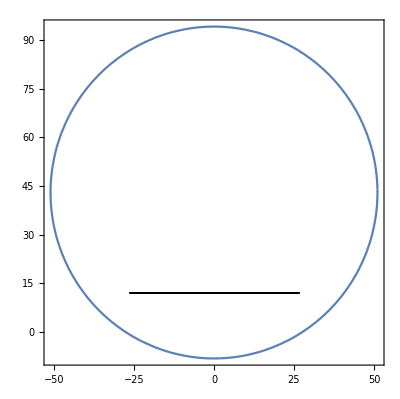

```mathematica
Show[ContourPlot[(x-0)^2+(y-43)^2==51.1^2,{x,-51.1,51.1},{y,-51.1+43,51.1+43},AspectRatio->Automatic],Graphics[{Line[{{ToExpression[axB],-1*ToExpression[ayB]},{ToExpression[axB1],-1*ToExpression[ayB]},{ToExpression[axB],-1*ToExpression[ayB]}}]}]](*unfinished:all parameters should be set from input file for complete phantom*)
```

```mathematica
NSolve[{(x-0)^2+(y-43)^2==51.1^2,x==ToExpression[axB]},{x,y}]
```

{{x→-26.4465,y→-0.724051},{x→-26.4465,y→86.7241}}

```mathematica
(* Source and Other *)
```

```mathematica
WriteLine[ipp,""]
```

```mathematica
WriteLine[ipp,"mode p"];
```

```mathematica
(*RDUM*)
```

```mathematica
(*RDUM 1 - radius of trajectory of the X-ray tube, cm*)RDUM1=60;
```

```mathematica
(*RDUM 2 - fan angle, degrees*)RDUM2=49.2;
```

```mathematica
(*RDUM 3 - start position of the scan on the z-axis, cm*)RDUM3=Zcent;
```

```mathematica
(*RDUM 4 scan range, cm;*)(*0 for axial;*)RDUM4=0;
```

```mathematica
(*RDUM 5 - actual beam width, cm*)RDUM5=1;(*1 is first try to do the calculation;3.5 for debug; was 2.6;*)
```

```mathematica
(*RDUM 6 - pitch of the axial acquisition*)(*0 for axial scan*)RDUM6=0;
```

```mathematica
(*RDUM 7 - type of the shaping filter used in the acquisition*)(*2 - small S filter 100 kV
10 - medium M filter 100 kV
12 - flat filter*)RDUM7=10;(*debug*)
```

```mathematica
(*RDUM 8 - Subscript[X, center]*)RDUM8=0;
```

```mathematica
(*RDUM 9 - Subscript[Y, center]*)RDUM9=5.78165;(*manually chosen for head scan*)
```

```mathematica
(*RDUM 10 - Subscript[n, source cell]*)RDUM10=198;
```

```mathematica
(dvsl (nsliMax)-Zcent)
```

0.

```mathematica
If[CT,WriteString[ipp,"RDUM "~~ToString[RDUM1]~~" "~~ToString[RDUM2]~~" "~~ToString[RDUM3]~~" "~~ToString[RDUM4]~~" "~~ToString[RDUM5]~~" "~~ToString[RDUM6]~~" "~~ToString[RDUM7]~~" "~~ToString[RDUM8]~~" "~~ToString[RDUM9]~~" "~~ToString[RDUM10]~~"\n"],www="c SOURCE \n"~~"sdef erg d1 par=2  pos="~~ToString[srcx]~~" "~~ToString[srcy]~~"   "~~ToString[(dvsl (nsliMax)-Zcent)] ~~vec~~" dir d4 \n";
WriteString[ipp,www];EEE=spectrum[[All,1]];int=spectrum[[All,2]];
Nisotopeline=Length[EEE];
si1Card="si1 A ";sp1Card="sp1 ";ccc=" ";

Do[aaa=EEE[[kk]];bbb=ToString[aaa,CharacterEncoding->"ASCII"];si1Card=StringJoin[si1Card,ccc,bbb];nnstring=StringLength[si1Card];If[nnstring>60,If[kk<Nisotopeline,si1Card=StringJoin[si1Card,"&"],Null];
Write[ipp,TextForm[si1Card]];si1Card=" ",Null];
Null,{kk,1,Nisotopeline}];
If[si1Card≠" ",Write[ipp,TextForm[si1Card]],Null];

Do[If[kk==1,aaa=FortranForm[Chop[SetPrecision[int[[kk]],4],5*10^-7]],If[kk>1,aaa=FortranForm[Chop[SetPrecision[int[[kk]],4],5*10^-7]],Null]];
bbb=ToString[aaa,CharacterEncoding->"ASCII"];sp1Card=StringJoin[sp1Card,ccc,bbb];nnstring=StringLength[sp1Card];If[nnstring>60,If[kk<Nisotopeline,sp1Card=StringJoin[sp1Card,"&"],Null];
Write[ipp,TextForm[sp1Card]];sp1Card=" ",Null];
Null,{kk,1,Nisotopeline}];
If[sp1Card≠" ",Write[ipp,TextForm[sp1Card]],Null];dir=N[Cos[ArcTan[√((AppertX[[1]]/2.)^2+(AppertZ[[1]]/2.)^2)/1./RIP[[1]]]]];;
WriteString[ipp,"si4 "~~ToString[dir]~~" 1.\n"]
WriteString[ipp,"sp4 -21 1\n"];];
```

```mathematica
(* Creation of Media *)
```

```mathematica
media0 = Import[Phantom<>"_media.dat","Table"]
```

{{1,6,7,8,11,12,15,16,17,19,20,26,53},{Tissues,to,be,used,in,the,Monte,Carlo,simulation:,H,C,N,O,Na,Mg,P,S,Cl,K,Ca,Fe,I},{No.,(%,by,mass)},{1,Teeth,2.2,9.5,2.9,42.1,0.,0.7,13.7,0.,0.,0.,28.9,0.,0.},{2,Mineral,bone,3.6,15.9,4.2,44.8,0.3,0.2,9.4,0.3,0.,0.,21.3,0.,0.},{3,Humeri,,upper,half,,spongiosa,8.7,36.6,2.5,42.2,0.2,0.1,3.,0.3,0.1,0.1,6.2,0.,0.},{4,Humeri,,lower,half,,spongiosa,9.6,47.3,1.7,34.1,0.2,0.,2.2,0.2,0.1,0.,4.6,0.,0.},{5,Lower,arm,bones,,spongiosa,9.6,47.3,1.7,34.1,0.2,0.,2.2,0.2,0.1,0.,4.6,0.,0.},{6,Hand,bones,,spongiosa,9.6,47.3,1.7,34.1,0.2,0.,2.2,0.2,0.1,0.,4.6,0.,0.},{7,Clavicles,,spongiosa,8.7,36.1,2.5,42.4,0.2,0.1,3.1,0.3,0.1,0.1,6.4,0.,0.},{8,Cranium,,spongiosa,8.1,31.7,2.8,45.1,0.2,0.1,3.7,0.3,0.1,0.1,7.8,0.,0.},{9,Femora,,upper,half,,spongiosa,10.4,49.6,1.8,34.9,0.1,0.,0.9,0.2,0.1,0.1,1.9,0.,0.},{10,Femora,,lower,half,,spongiosa,9.6,47.3,1.7,34.1,0.2,0.,2.2,0.2,0.1,0.,4.6,0.,0.},{11,Lower,leg,bones,,spongiosa,9.6,47.3,1.7,34.1,0.2,0.,2.2,0.2,0.1,0.,4.6,0.,0.},{12,Foot,bones,,spongiosa,9.6,47.3,1.7,34.1,0.2,0.,2.2,0.2,0.1,0.,4.6,0.,0.},{13,Mandible,,spongiosa,8.7,35.7,2.6,42.9,0.2,0.1,3.,0.3,0.1,0.1,6.3,0.,0.},{14,Pelvis,,spongiosa,9.6,40.6,2.5,41.2,0.1,0.,1.8,0.2,0.1,0.1,3.8,0.,0.},{15,Ribs,,spongiosa,9.7,38.1,2.8,44.5,0.1,0.,1.4,0.2,0.2,0.1,2.8,0.1,0.},{16,Scapulae,,spongiosa,9.4,40.6,2.4,40.4,0.1,0.,2.2,0.2,0.1,0.1,4.5,0.,0.},{17,Cervical,spine,,spongiosa,9.2,35.1,2.9,45.8,0.1,0.,2.1,0.2,0.2,0.1,4.3,0.,0.},{18,Thoracic,spine,,spongiosa,9.8,38.6,2.8,44.2,0.1,0.,1.3,0.2,0.2,0.1,2.6,0.1,0.},{19,Lumbar,spine,,spongiosa,8.8,32.9,3.,46.6,0.1,0.1,2.6,0.3,0.1,0.1,5.4,0.,0.},{20,Sacrum,,spongiosa,10.2,41.,2.7,43.3,0.1,0.,0.7,0.2,0.2,0.1,1.4,0.1,0.},{21,Sternum,,spongiosa,9.9,39.2,2.8,43.9,0.1,0.,1.2,0.2,0.2,0.1,2.3,0.1,0.},{22,Humeri,and,femora,,upper,halves,,medullary,cavity,11.5,63.7,0.7,23.8,0.1,0.,0.,0.1,0.1,0.,0.,0.,0.},{23,Humeri,and,femora,,lower,halves,,medullary,cavity,11.5,63.7,0.7,23.8,0.1,0.,0.,0.1,0.1,0.,0.,0.,0.},{24,Lower,arm,bones,,medullary,cavity,11.5,63.7,0.7,23.8,0.1,0.,0.,0.1,0.1,0.,0.,0.,0.},{25,Lower,leg,bones,,medullary,cavity,11.5,63.7,0.7,23.8,0.1,0.,0.,0.1,0.1,0.,0.,0.,0.},{26,Cartilage,9.6,9.9,2.2,74.4,0.5,0.,2.2,0.9,0.3,0.,0.,0.,0.},{27,Skin,10.,19.9,4.2,65.,0.2,0.,0.1,0.2,0.3,0.1,0.,0.,0.},{28,Blood,10.2,11.,3.3,74.5,0.1,0.,0.1,0.2,0.3,0.2,0.,0.1,0.},{29,Muscle,tissue,10.2,14.2,3.4,71.1,0.1,0.,0.2,0.3,0.1,0.4,0.,0.,0.},{30,Liver,10.2,13.1,3.1,72.4,0.2,0.,0.2,0.3,0.2,0.3,0.,0.,0.},{31,Pancreas,10.5,15.7,2.4,70.5,0.2,0.,0.2,0.1,0.2,0.2,0.,0.,0.},{32,Brain,10.7,14.4,2.2,71.3,0.2,0.,0.4,0.2,0.3,0.3,0.,0.,0.},{33,Heart,10.4,13.8,2.9,71.9,0.1,0.,0.2,0.2,0.2,0.3,0.,0.,0.},{34,Eyes,9.7,18.3,5.4,66.,0.1,0.,0.1,0.3,0.1,0.,0.,0.,0.},{35,Kidneys,10.3,12.5,3.1,73.,0.2,0.,0.2,0.2,0.2,0.2,0.1,0.,0.},{36,Stomach,10.5,11.4,2.5,75.,0.1,0.,0.1,0.1,0.2,0.1,0.,0.,0.},{37,Small,intestine,10.5,11.4,2.5,75.,0.1,0.,0.1,0.1,0.2,0.1,0.,0.,0.},{38,Large,intestine,10.5,11.4,2.5,75.,0.1,0.,0.1,0.1,0.2,0.1,0.,0.,0.},{39,Spleen,10.3,11.2,3.2,74.3,0.1,0.,0.2,0.2,0.2,0.3,0.,0.,0.},{40,Thyroid,10.4,11.8,2.5,74.5,0.2,0.,0.1,0.1,0.2,0.1,0.,0.,0.1},{41,Urinary,bladder,10.5,9.6,2.6,76.1,0.2,0.,0.2,0.2,0.3,0.3,0.,0.,0.},{42,Ovaries,10.5,9.4,2.5,76.6,0.2,0.,0.2,0.2,0.2,0.2,0.,0.,0.},{43,Adrenals,10.4,22.8,2.8,63.,0.1,0.,0.2,0.3,0.2,0.2,0.,0.,0.},{44,Oesophagus,10.4,22.2,2.8,63.6,0.1,0.,0.2,0.3,0.2,0.2,0.,0.,0.},{45,Gallbladder,,Pituitary,gland,,Trachea,,Thymus,,Tonsils,,Ureters,,...,10.5,23.5,2.8,62.2,0.1,0.,0.2,0.3,0.2,0.2,0.,0.,0.},{46,Uterus,10.5,28.6,2.5,57.6,0.1,0.,0.2,0.2,0.1,0.2,0.,0.,0.},{47,Lymph,10.8,4.2,1.1,83.1,0.3,0.,0.,0.1,0.4,0.,0.,0.,0.},{48,Breast,(mammary,gland),11.4,46.1,0.5,42.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{49,Adipose,tissue,11.4,58.9,0.7,28.7,0.1,0.,0.,0.1,0.1,0.,0.,0.,0.},{50,Lung,tissue,(compressed,lungs),10.3,10.7,3.2,74.6,0.2,0.,0.2,0.3,0.3,0.2,0.,0.,0.},{51,Gastro-intestinal,tract,-,contents,10.,22.2,2.2,64.4,0.1,0.,0.2,0.3,0.1,0.4,0.1,0.,0.},{52,Urine,10.7,0.3,1.,87.3,0.4,0.,0.1,0.,0.,0.2,0.,0.,0.},{53,Air,0.,0.,80.,20.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
If[StringPosition[Phantom,"A"]≠{},media={media0[[1]],media0[[2]],media0[[3]]},media={Table[StringSplit[media0[[1,i]],_?LetterQ][[1]],{i,3,Length[media0[[1]]]-2}]}];
```

```mathematica
If[StringPosition[Phantom,"A"]≠{},Do[   
 Do[ If[ numMed[[ik]]==media0[[io]][[1]],AppendTo[ media,media0[[io]]],Null]     ,{ik,1,Length[numMed]}]
,{io,4,Length[media0]}],Do[   
 Do[ If[ numMed[[ik]]==media0[[io]][[1]],AppendTo[ media,media0[[io]]],Null]     ,{ik,1,Length[numMed]}]
,{io,2,Length[media0]}]];
```

```mathematica
WriteString[ipp,"c MEDIA\n"];(*tmpLen is Viarenich way: fixed writing first element, ruined writing materials with long descriptions*)
(*Do[tmpLen=Length[media[[im]]];
za="m"~~ToString[media[[im]][[1]]]; word="  $ ";
Do[
 If[media[[im]][[iz]]≠ 0 &&NumberQ[ media[[im]][[iz]]],ww="  "~~ToString[media[[1]][[iz-2-tmpLen+15]] ]~~"000"~~" -"~~ToString[media[[im]][[iz]] ] ;za=za~~ww;
If[StringLength[za] ≥ 67,za=za~~"\n";
WriteString[ipp,za];za="     ",Null],
If[NumberQ[ media[[im]][[iz]]]==  False,word=word~~ToString[media[[im]][[iz]]],Null]]
 ,{iz,2,Length[media[[1]]]+2}];
za=za~~word~~"\n";
WriteString[ipp,za];
Null,{im,4,Length[media]}]*)
```

```mathematica
If[StringPosition[Phantom,"A"]≠{},Do[tmpLen=Length[media[[im]]];za="m"~~ToString[media[[im]][[1]]]; word="  $ ";tmpMedia=Take[media[[im]],-13];Do[If[tmpMedia[[iz]]≠ 0 ,ww="  "~~ToString[media[[1,iz]]]~~"000"~~" -"~~ToString[tmpMedia[[iz]]];za=za~~ww;If[StringLength[za] ≥ 67,za=za~~"\n";WriteString[ipp,za];
za="   ",Null]],{iz,13}];
Do[
If[NumberQ[ media[[im]][[iz]]]&&media[[im]][[iz]]≠ 0 ,Null,
If[NumberQ[ media[[im]][[iz]]]==  False,word=word~~ToString[media[[im]][[iz]]],Null]]
 ,{iz,2,Length[media[[1]]+2]}];za=za~~word~~"\n";
WriteString[ipp,za];
Null,{im,4,Length[media]}],Do[tmpLen=Length[media[[im]]];za="m"~~ToString[media[[im]][[1]]]; word=" $";tmpMedia=Take[media[[im]],{-14,-2}];Do[If[tmpMedia[[iz]]≠ 0 ,ww="  "~~ToString[media[[1,iz]]]~~"000"~~" -"~~ToString[tmpMedia[[iz]]];za=za~~ww;If[StringLength[za] ≥ 67,za=za~~"\n";WriteString[ipp,za];
za="   ",Null]],{iz,13}];If[za=="   ", za="";word="c ", word=" $"];
(*comment*)Do[
If[NumberQ[ media[[im]][[iz]]]&&media[[im]][[iz]]≠ 0 ,Null,
If[NumberQ[ media[[im]][[iz]]]==  False,word=word~~ToString[media[[im]][[iz]]],Null]]
 ,{iz,2,Length[media[[1]]+2]}];za=za~~word~~"\n";
WriteString[ipp,za];
Null,{im,2,Length[media]}];Print["pediatric phantom"]]
```

```mathematica
If[CT,WriteString[ipp,"m54 6000 -1 $Carbon (fiber)\n"]];
```

```mathematica
If[TrueQ[CT],Print["CT mode, calculator not enabled"],WriteString[ipp,"m80 82000 -1 $ Lead for curtains\n"]]
```

CT mode, calculator not enabled

```mathematica
(* Create end of input file  *)
```

```mathematica
WriteLine[ipp,"c tally "]
```

```mathematica
If[Length[cell]>1,work="fm6 1e12\n*f6:p ";workcells="";Do[  ww=cell[[ic]][[1]]; If[ww==140,,workcells=workcells~~" "~~ToString[ww]];
,{ic,1,Length[cell]}];WriteString[ipp,work];WriteString[ipp,StringTrim[WriteMCNPCard[workcells]]];WriteString[ipp,"\n*f8:p "];WriteString[ipp,StringTrim[WriteMCNPCard[workcells]]];WriteString[ipp,"\nf4:p "];WriteLine[ipp,StringTrim[WriteMCNPCard[workcells]]],Null]
```

```mathematica
WriteLine[ipp,"nps "~~ToString[200000]];
```

```mathematica
WriteLine[ipp,"prdmp 2j 1 r"];
```

```mathematica
Streams[]
```

{OutputStream[…],OutputStream[…],OutputStream[…],OutputStream[…]}

```mathematica
Close[ipp]
```

AF_168.432